√2 π^(3/4) (-(ⅇ^(-ϵ/(k To+k To z)) π^(3/4) ((k m To (1+z))/h^2)^(3/2))/nH+√((ⅇ^(-(2 ϵ)/(k To+k To z)) ((k^3 m^3 π^(3/2) To^3 (1+z)^3)/h^6+√2 ⅇ^(ϵ/(k To+k To z)) nH ((k m To (1+z))/h^2)^(3/2)))/nH^2))

3.3×10^-31 (1+z)^3

1

1.

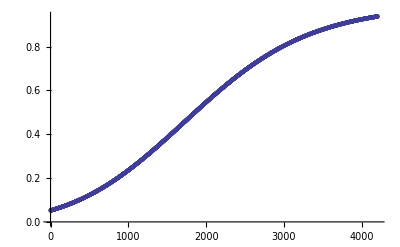

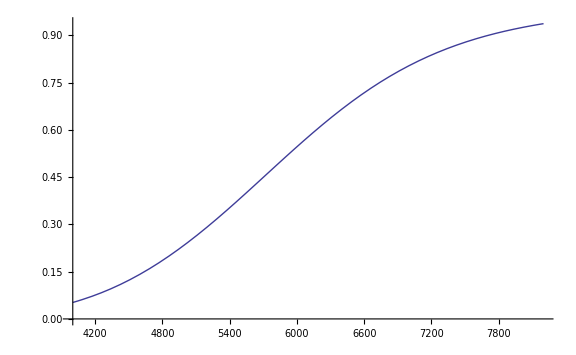

```mathematica
Remove["Global`*"]

Saha[T_]=((2 π m k T)/h^2)^(3/2)Exp[-ϵ/(k T)];
Saha[z_]=Saha[To(1+z)];

f[x_]=(-x/nH+√((x/nH)^2+4(x/nH)))/2;
f[z_]=f[x]/.x->Saha[z] ;
f[z]//FullSimplify
hcgs=6.62606957*10^-27;
hev=4.135667516*10^-15;
kcgs=1.3806488*10^-16 ;
kev=8.6173324*10^-5;
ccgs=2.99792458*10^10;
mcgs=9.10938291*10^-28;
h=hev;k=kev;c=ccgs;m=mcgs;
To=2.725;
ϵ=13.6 (kev/kev);
nH=.75(4.4*10^-31)(1+z)^3
nH=1
Limit[f[z],z->∞]
points=Table[f[z],{z,4000,8200}];
ListPlot[points]
Plot[f[z],{z,4000,8200},ImageSize->Large,PerformanceGoal->"Quality"]
```